```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 5900 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[rM]
rM = { x[t] , l }
```

{x[t],l}

```mathematica
D[rM, t]
```

{x'[t],0}

```mathematica
D[rM, t] . D[rM, t]
```

x'[t]^2

```mathematica
Clear[rm]
rm = { x[t] + l Sin[θ[t]] , l - l Cos[θ[t]] }
```

{l Sin[θ[t]]+x[t],l-l Cos[θ[t]]}

```mathematica
D[rm, t]
```

{x'[t]+l Cos[θ[t]] θ'[t],l Sin[θ[t]] θ'[t]}

```mathematica
D[rm, t] . D[rm, t]
```

l^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+l Cos[θ[t]] θ'[t])^2

```mathematica
D[rm, t] . D[rm, t]  // Expand
```

x'[t]^2+2 l Cos[θ[t]] x'[t] θ'[t]+l^2 Cos[θ[t]]^2 θ'[t]^2+l^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[rm, t] . D[rm, t]  // Expand  // Simplify
```

x'[t]^2+2 l Cos[θ[t]] x'[t] θ'[t]+l^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 M ( D[rM, t] . D[rM, t]  ) + 1/2 m ( D[rm, t] . D[rm, t]  // Expand  // Simplify  )
```

1/2 M x'[t]^2+1/2 m (x'[t]^2+2 l Cos[θ[t]] x'[t] θ'[t]+l^2 θ'[t]^2)

```mathematica
rM
rM[[2]]
```

{x[t],l}

l

```mathematica
Clear[VM]
VM = M g rM[[2]]
```

g l M

```mathematica
rm
rm[[2]]
```

{l Sin[θ[t]]+x[t],l-l Cos[θ[t]]}

l-l Cos[θ[t]]

```mathematica
Clear[Vm]
Vm = m g rm[[2]]
```

g m (l-l Cos[θ[t]])

```mathematica
Clear[V]
V = VM + Vm + 1/2 k x[t]^2
```

g l M+g m (l-l Cos[θ[t]])+1/2 k x[t]^2

```mathematica
Clear[ℒ]
ℒ = T- V
```

-g l M-g m (l-l Cos[θ[t]])-1/2 k x[t]^2+1/2 M x'[t]^2+1/2 m (x'[t]^2+2 l Cos[θ[t]] x'[t] θ'[t]+l^2 θ'[t]^2)

```mathematica
Clear[q]
q = { x[t] , θ[t] }
```

{x[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ]  // Expand 
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ] // Expand
```

k x[t]-l m Sin[θ[t]] θ'[t]^2+m x''[t]+M x''[t]+l m Cos[θ[t]] θ''[t]

g l m Sin[θ[t]]+l m Cos[θ[t]] x''[t]+l^2 m θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ] , 
{ i, 1, 2 } ]  // Expand // Simplify // TableForm
```

k x[t]-l m Sin[θ[t]] θ'[t]^2+m x''[t]+M x''[t]+l m Cos[θ[t]] θ''[t]
l m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+l θ''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-k x[t]+l m Sin[θ[t]] θ'[t]^2-m x''[t]-M x''[t]-l m Cos[θ[t]] θ''[t]==0
-l m (g Sin[θ[t]]+Cos[θ[t]] x''[t]+l θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
k-> 20 ,
l-> 1 , 
m -> 5 , 
M-> 30 , 
g-> 9.8  } ;
parameters // TableForm
```

k→20
l→1
m→5
M→30
g→9.8

```mathematica
eqs /. parameters // Expand // TableForm
```

-20 x[t]+5 Sin[θ[t]] θ'[t]^2-35 x''[t]-5 Cos[θ[t]] θ''[t]==0
-49. Sin[θ[t]]-5 Cos[θ[t]] x''[t]-5 θ''[t]==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0.5 , 
x'[0] == 0 , 
θ[0]  == π/12 ,
θ'[0] == 0 }  ;
ics // TableForm
```

x[0]==0.5
x'[0]==0
θ[0]==π/12
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ] ]
```

{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]]  , { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

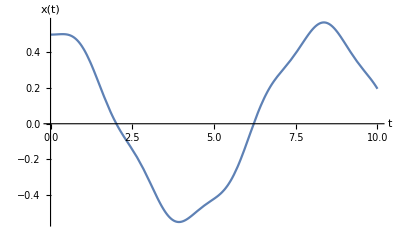

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t , q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```

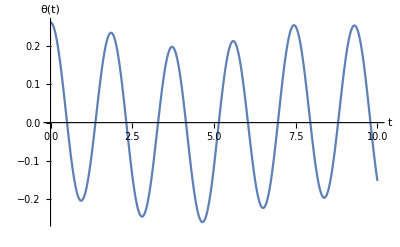

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 10 }, AxesLabel-> { t , q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```